# Hierarchical control of two-site system

Table of Contents 
1. Definition of System Model
2. Partial Linearization and Design of Lower-level Controller
3. Design of Upper-level MPC controller
4. Simulation of the Closed-loop System

## 1. Definition of System Model

### Model equations

```mathematica
Subscript[fg, 1][u_,V_,Pg_,Pgg_,i_]:= 1/Subscript[tv, i] (-Subscript[V, i]+(1-Subscript[α, i])Subscript[Vce, i]+Subscript[α, i]) 
Subscript[fg, 2][u_,V_,Pg_,Pgg_,i_]:=1/Subscript[tf, i](Subscript[V, i] - Subscript[Pg, i])
Subscript[fg, 3][u_,V_,Pg_,Pgg_,i_]:=1/Subscript[tcd, i](Subscript[Pg, i] - Subscript[Pgg, i])
pm[Pgg_,α_,i_]:=Subscript[ke, i] 1/(1-Subscript[α, i])( Subscript[Pgg, i]-Subscript[α, i])
q[Pg_,i_]:=Subscript[kh, i] 1/(1+Subscript[β, i])(Subscript[Pg, i]+Subscript[β, i])
Subscript[fe, 1][δ_,ω_,i_,j_]:=1/Subscript[te, i] Subscript[ω, i]
Subscript[fe, 2][δ_,ω_,i_,j_]:=1/Subscript[te, i](pm[Pgg,α,i] -Subscript[Da, i] Subscript[ω, i] -Subscript[Ee, i]^2 Subscript[G, i,i]-Subscript[Ee, i] Subscript[Ee, 0](Subscript[B, i,0] Sin[Subscript[δ, i]]+Subscript[G, i,0] Cos[Subscript[δ, i]]) -Subscript[Ee, i] Subscript[Ee, j](Subscript[B, i,j] Sin[Subscript[δ, i]-Subscript[δ, j]] -Subscript[G, i,j] Cos[Subscript[δ, i]-Subscript[δ, j]])) (* Da and Ee are used for distiuguish with Mathematica function D and E *)
Subscript[fh, 1][p1_,p2_,U_]:=1/Subscript[th, 1](q[Pg,1]- Subscript[QL, 1] -π/4 Subscript[h, c] Subscript[ρ, s] U)
Subscript[fh, 2][p1_,p2_,U_]:=1/Subscript[th, 2](q[Pg,2]- Subscript[QL, 2] +π/4 Subscript[h, c] Subscript[ρ, s] U)
Subscript[fh, 3][p1_,p2_,U_]:=1/Subscript[th, 3]((p1-p2)/Subscript[ρ, s]-(λ L)/(2d)U U )  (*U is assumed to be positive*)
Subscript[P, inf][δ1_,ω1_,δ2_,ω2_]:=(-Subscript[G, 0,0] Subscript[Ee, 0]^2+Subscript[Ee, 1] Subscript[Ee, 0](Subscript[B, 1,0] Sin[δ1]-Subscript[G, 1,0] Cos[δ1])+Subscript[Ee, 2] Subscript[Ee, 0](Subscript[B, 2,0] Sin[δ2]-Subscript[G, 2,0] Cos[0-δ2]));
Subscript[Q, 12][p1_,p2_,U_]:= π/4 Subscript[h, c] Subscript[ρ, s] U ;
Subscript[p, mean][p1_,p2_,U_]:= (p1+p2)/2 ;
```

### State space model

```mathematica
n=13;
xt=Table[Subscript[x, i][t],{i,n}];
xfun={x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_}; (* 状態変数xについての関数を定義する時に使用 *)
xarg={x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13}; (* 定義した関数を呼び出すときに使用 *)
affine[xfun]=Join[
Table[Subscript[fg, i][u,V,Pg,Pgg,1],{i,3} ] (* gas turbine *),
Table[Subscript[fg, i][u,V,Pg,Pgg,2],{i,3} ] ,
Table[Subscript[fe, i][δ,ω,1,2],{i,2}] (*generator*),
Table[Subscript[fe, i][δ,ω,2,1],{i,2}],
Table[Subscript[fh, i][Subscript[p, 1],Subscript[p, 2],U],{i,3}](*heat system*)
] /. Join[{Subscript[V, 1]->x1,Subscript[Pg, 1]->x2,Subscript[Pgg, 1]->x3},{Subscript[V, 2]->x4,Subscript[Pg, 2]->x5,Subscript[Pgg, 2]->x6},{Subscript[δ, 1]->x7,Subscript[ω, 1]->x8,Subscript[δ, 2]->x9,Subscript[ω, 2]->x10}, {Subscript[p, 1]->x11,Subscript[p, 2]->x12,U->x13},{Subscript[Vce, 1]->u1,Subscript[Vce, 2]->u2}];
f[xfun]=affine[xarg]/.{u1->0,u2->0};
Subscript[g, 1][xfun]=Simplify[affine[xarg]-f[xarg]]/.{u1->1,u2->0};
Subscript[g, 2][xfun]=Simplify[affine[xarg]-f[xarg]]/.{u1->0,u2->1};
g[xfun]=Transpose[{Subscript[g, 1][xarg],Subscript[g, 2][xarg]}];
Subscript[h, 1][xfun]=Subscript[P, inf][x7,x8,x9,x10];
Subscript[h̄, 2][xfun]=Subscript[p, mean][x11,x12,x13];
Subscript[h, 2][xfun]=Subscript[Q, 12][x11,x12,x13];
h[xfun]={Subscript[h, 1][xarg],Subscript[h̄, 2][xarg]};
```

```mathematica
MatrixForm[f[xarg]]+MatrixForm[g[xarg]]
MatrixForm[h[xarg]]
```

((1-α_1)/tv_1 | 0
0 | 0
0 | 0
0 | (1-α_2)/tv_2
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)+((-x1+α_1)/tv_1
(x1-x2)/tf_1
(x2-x3)/tcd_1
(-x4+α_2)/tv_2
(x4-x5)/tf_2
(x5-x6)/tcd_2
x8/te_1
(-x8 Da_1+(ke_1 (x3-α_1))/(1-α_1)-Ee_0 Ee_1 (Sin[x7] B_(1,0)+Cos[x7] G_(1,0))-Ee_1^2 G_(1,1)-Ee_1 Ee_2 (Sin[x7-x9] B_(1,2)-Cos[x7-x9] G_(1,2)))/te_1
x10/te_2
(-x10 Da_2+(ke_2 (x6-α_2))/(1-α_2)-Ee_0 Ee_2 (Sin[x9] B_(2,0)+Cos[x9] G_(2,0))-Ee_1 Ee_2 (-Sin[x7-x9] B_(2,1)-Cos[x7-x9] G_(2,1))-Ee_2^2 G_(2,2))/te_2
(-QL_1+(kh_1 (x2+β_1))/(1+β_1)-1/4 π x13 h_c ρ_s)/th_1
(-QL_2+(kh_2 (x5+β_2))/(1+β_2)+1/4 π x13 h_c ρ_s)/th_2
(-(L x13^2 λ)/(2 d)+(x11-x12)/ρ_s)/th_3)

(-Ee_0^2 G_(0,0)+Ee_0 Ee_1 (Sin[x7] B_(1,0)-Cos[x7] G_(1,0))+Ee_0 Ee_2 (Sin[x9] B_(2,0)-Cos[x9] G_(2,0))
(x11+x12)/2)

### Setting of parameters

```mathematica
ratedvalues = {Subscript[Q, r]-> 1000*10^3,Subscript[h, r]->(800*10^3)/4.16,Subscript[ρ, r]-> 4.16,Subscript[e, 1]->3800,Subscript[e, 2]->3800,L->200,d->0.2};
parameter=Flatten[Join[Table[
{Subscript[tv, i]->0.05,Subscript[tf, i]->0.4,Subscript[tcd, i]->0.1,Subscript[α, i]->0.23,Subscript[β, i]->0},{i,2}],
{Subscript[ke, 1]->1.5,Subscript[ke, 2]->0.6,Subscript[kh, 1]->6,Subscript[kh, 2]->6},
{ Subscript[te, 1]-> 0.23,Subscript[te, 2]->0.23,Subscript[Da, 1]->0.05,Subscript[Da, 2]->0.05,Subscript[Ee, 0]->1,Subscript[Ee, 1]->1,Subscript[Ee, 2]->1},{Subscript[B, 1,0]->1,Subscript[B, 2,0]->1,Subscript[B, 1,2]->0.5,Subscript[B, 2,1]->0.5,Subscript[G, 0,0]->0,Subscript[G, 1,1]->0.0,Subscript[G, 2,2]->0,Subscript[G, 1,0]->0,Subscript[G, 2,0]->0,Subscript[G, 1,2]->0,Subscript[G, 2,1]->0},
{Subscript[QL, 1]->2,Subscript[QL, 2]->5,λ->0.016,L->200,d->0.2},
{Subscript[th, 1]->(Subscript[Q, r] Subscript[e, 1])/(d^4 Subscript[h, r]^2 Subscript[ρ, r]),Subscript[th, 2]->(Subscript[Q, r] Subscript[e, 1])/(d^4 Subscript[h, r]^2 Subscript[ρ, r]),Subscript[th, 3]->(d^2 L Subscript[ρ, r] Subscript[h, r])/Subscript[Q, r],Subscript[h, c]->(2047*10^3)/Subscript[h, r],Subscript[ρ, s]-> 4.16/Subscript[ρ, r]}/. ratedvalues
]
]
Subscript[w, rated]= Subscript[Q, r]/(d^2*Subscript[h, r]*Subscript[ρ, r])/.ratedvalues
Subscript[p, rated]= Subscript[ρ, r]*Subscript[w, rated]^2 /. ratedvalues
```

{tv_1→0.05,tf_1→0.4,tcd_1→0.1,α_1→0.23,β_1→0,tv_2→0.05,tf_2→0.4,tcd_2→0.1,α_2→0.23,β_2→0,ke_1→1.5,ke_2→0.6,kh_1→6,kh_2→6,te_1→0.23,te_2→0.23,Da_1→0.05,Da_2→0.05,Ee_0→1,Ee_1→1,Ee_2→1,B_(1,0)→1,B_(2,0)→1,B_(1,2)→0.5,B_(2,1)→0.5,G_(0,0)→0,G_(1,1)→0.,G_(2,2)→0,G_(1,0)→0,G_(2,0)→0,G_(1,2)→0,G_(2,1)→0,QL_1→2,QL_2→5,λ→0.016,L→200,d→0.2,th_1→15.4375,th_2→15.4375,th_3→6.4,h_c→10.6444,ρ_s→1.}

31.25

4062.5

### Calculation of an equilibrium point

```mathematica
floweq=Join[f[Table[Subscript[x, i],{i,13}]]+g[Table[Subscript[x, i],{i,13}]].{Subscript[u, 1],Subscript[u, 2]},{Subscript[h, 1][Table[Subscript[x, i],{i,13}]]-Subscript[P, e,ref], Subscript[h̄, 2][Table[Subscript[x, i],{i,13}]]-Subscript[p, ref]}]/.parameter /.{Subscript[P, e,ref]-> 1.0,Subscript[p, ref]->0.00};
ep=FindRoot[floweq==0,
{{Subscript[x, 1],0.7},{Subscript[x, 2],0.7},{Subscript[x, 3],0.7},{Subscript[x, 4],0.7},{Subscript[x, 5],0.7},{Subscript[x, 6],0.7},{Subscript[x, 7],0.3},{Subscript[x, 8],0},{Subscript[x, 9],0.3},{Subscript[x, 10],0},{Subscript[x, 11],0},{Subscript[x, 12],0},{Subscript[x, 13],0}
,{Subscript[u, 1],0.7},{Subscript[u, 2],0.7}}]
equilibriumpoint = Table[Subscript[x, i],{i,13}]/. ep;
Φ[equilibriumpoint]/.parameter  (* (ξ, η) at equilibrium point *)
```

{x_1→0.614444,x_2→0.614444,x_3→0.614444,x_4→0.552222,x_5→0.552222,x_6→0.552222,x_7→0.663523,x_8→0.,x_9→0.394237,x_10→0.,x_11→0.162816,x_12→-0.162816,x_13→0.201752,u_1→0.499278,u_2→0.41847}

Φ[{0.614444,0.614444,0.614444,0.552222,0.552222,0.552222,0.663523,0.,0.394237,0.,0.162816,-0.162816,0.201752}]

## 2. Partial Linearization and Design of Local Controller

#### Lie derivative of function h(x) along vector field f(x)

```mathematica
Ld[f_,h_,x_]:= D[h[x],{x}].f[x]
```

#### Calculate ξ variables for h_1

```mathematica
Lfh1[xfun]=Ld[f,Subscript[h, 1],xarg];
Lgh1[xfun]={Ld[Subscript[g, 1],Subscript[h, 1],xarg],Ld[Subscript[g, 2],Subscript[h, 1],xarg]}
```

{0,0}

```mathematica
Lf2h1[xfun]=Ld[f,Lfh1,xarg];
LgLfh1[xfun]={Ld[Subscript[g, 1],Lfh1,xarg],Ld[Subscript[g, 2],Lfh1,xarg]}
```

{0,0}

```mathematica
Lf3h1[xfun]=Ld[f,Lf2h1,xarg];
LgLf2h1[xfun]={Ld[Subscript[g, 1],Lf2h1,xarg],Ld[Subscript[g, 2],Lf2h1,xarg]}
```

{0,0}

```mathematica
Lf4h1[xfun]=Ld[f,Lf3h1,xarg];
LgLf3h1[xfun]={Ld[Subscript[g, 1],Lf3h1,xarg],Ld[Subscript[g, 2],Lf3h1,xarg]}
```

{0,0}

```mathematica
Lf5h1[xfun]=Ld[f,Lf4h1,xarg];
LgLf4h1[xfun]={Ld[Subscript[g, 1],Lf4h1,xarg],Ld[Subscript[g, 2],Lf4h1,xarg]}
```

{(Ee_0 Ee_1 ke_1 (Cos[x7] B_(1,0)+Sin[x7] G_(1,0)))/(tcd_1 te_1^2 tf_1 tv_1),(Ee_0 Ee_2 ke_2 (Cos[x9] B_(2,0)+Sin[x9] G_(2,0)))/(tcd_2 te_2^2 tf_2 tv_2)}

#### Calculate ξ variables for h_2

```mathematica
Lfh2[xfun]=Ld[f,Subscript[h̄, 2],xarg]
Lgh2[xfun]={Ld[Subscript[g, 1],Subscript[h̄, 2],xarg],Ld[Subscript[g, 2],Subscript[h̄, 2],xarg]}
```

(-QL_1+(kh_1 (x2+β_1))/(1+β_1)-1/4 π x13 h_c ρ_s)/(2 th_1)+(-QL_2+(kh_2 (x5+β_2))/(1+β_2)+1/4 π x13 h_c ρ_s)/(2 th_2)

{0,0}

```mathematica
Lf2h2[xfun]=Ld[f,Lfh2,xarg];
LgLfh2[xfun]={Ld[Subscript[g, 1],Lfh2,xarg],Ld[Subscript[g, 2],Lfh2,xarg]}
```

{0,0}

```mathematica
Lf3h2[xfun]=Ld[f,Lf2h2,xarg];
LgLf2h2[xfun]={Ld[Subscript[g, 1],Lf2h2,xarg],Ld[Subscript[g, 2],Lf2h2,xarg]}
```

{(kh_1 (1-α_1))/(2 tf_1 th_1 tv_1 (1+β_1)),(kh_2 (1-α_2))/(2 tf_2 th_2 tv_2 (1+β_2))}

#### Vector relative degree and coordinate transformation

```mathematica
ξ[xfun]={{Subscript[h, 1][xarg],Lfh1[xarg],Lf2h1[xarg],Lf3h1[xarg],Lf4h1[xarg]},{Subscript[h̄, 2][xarg],Lfh2[xarg],Lf2h2[xarg]}};
γ=Map[Length,ξ[xarg]]
A[xfun]={LgLf4h1[xarg], LgLf2h2[xarg]};
b[xfun]={Lf5h1[xarg], Lf3h2[xarg]};
```

{5,3}

```mathematica
η[xfun]={x3,x7,x8,x11-x12,x13};
r[xfun]=Join[f[xarg]⟦{3,7,8}⟧,(f[xarg]⟦{11}⟧-f[xarg]⟦{12}⟧) , f[xarg]⟦{13}⟧];
dr[xfun]=D[r[xarg], {xarg}];
Φ[xfun]=Join[ξ[xarg]⟦1⟧,ξ[xarg]⟦2⟧,η[xarg]];
dΦ[xfun]=D[Φ[xarg], {xarg}];
MatrixRank[dΦ[xarg]]
```

13

```mathematica
dΦ[xfun][[1,13]]
```

0

#### Singularity of decoupling matrix and det(dΦ)

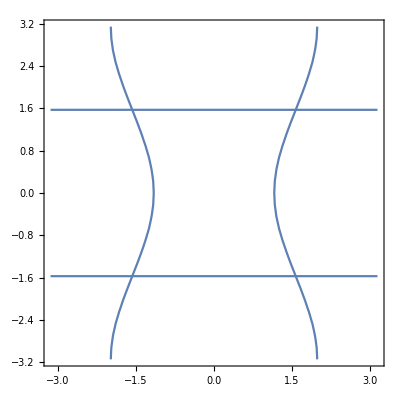

```mathematica
detA[xfun]=Det[A[xarg]]/.parameter;
detdΦ[xfun]= Det[dΦ[xarg]] /. parameter
singA=ContourPlot[detA[xarg]==0,{x7,-π,π},{x9,-π,π}];
singDΦ = ContourPlot[detdΦ[xarg]==0,{x7,-π,π},{x9,-π,π}];
Show[singA, singDΦ]
```

### Design of local Controller

```mathematica
po1=2.5;po2=0.25;
poles={Expand[(s+po1)^5],Expand[( s+po2)^3]};coef={CoefficientList[poles⟦1⟧,{s}],CoefficientList[poles⟦2⟧,{s}]};
```

```mathematica
fuelInput[x_,xiref_]:=Module[{stabilize,v,signal},stabilize={Table[coef⟦1,j⟧ (ξ[x]⟦1,j⟧-xiref⟦1,j⟧),{j,γ⟦1⟧}],Table[coef⟦2,j⟧ (ξ[x]⟦2,j⟧-xiref⟦2,j⟧),{j,γ⟦2⟧}]};v={-Total[stabilize⟦1⟧],-Total[stabilize⟦2⟧]};signal=Inverse[A[x]].{xiref⟦1,γ⟦1⟧+1⟧-Lf5h1[x]+v⟦1⟧,xiref⟦2,γ⟦2⟧+1⟧-Lf3h2[x]+v⟦2⟧}];
fuelInput[equilibriumpoint,{{1.0,0,0,0,0,0},{0,0,0,0}}]/.parameter
```

{0.499278,0.41847}

### Simulation of local Controller

```mathematica
CalLocalRes[x0_,v1_,v2_,tspan_] := Module[{t,xt,ξref,vectorfield,initconditions,equation,trajectory},
xt = Table[Subscript[x, i][t],{i,n}]; (* state variables *)
ξref={{v1,0,0,0,0,0},{v2,0,0,0}}; (* reference for local contoller *)
vectorfield=f[xt]+Subscript[g, 1][xt] fuelInput[xt,ξref]⟦1⟧+Subscript[g, 2][xt] fuelInput[xt,ξref]⟦2⟧/.parameter ;equation=Table[Subscript[x, i]'[t]==vectorfield⟦i⟧,{i,n}]; 
initconditions = Table[Subscript[x, i][0]==x0[[i]],{i,n}];
trajectory=NDSolve[Join[equation,initconditions],Table[Subscript[x, i],{i,n}],{t,0,tspan}] (* return solution of NDSolve*)
] 
Flatten[Table[Subscript[x, i][2.0],{i,n}]]/.CalLocalRes[equilibriumpoint,1.0,0,2.0] (* final value *)
(* Plot[Subscript[x, 1][t]/.parameter/.CalLocalRes[equilibriumpoint,1.0,0],{t,0.0,Tspan}] *)
```

{{0.614444,0.614444,0.614444,0.552222,0.552222,0.552222,0.663523,-1.489×10^-12,0.394237,1.27981×10^-12,0.162816,-0.162816,0.201752}}

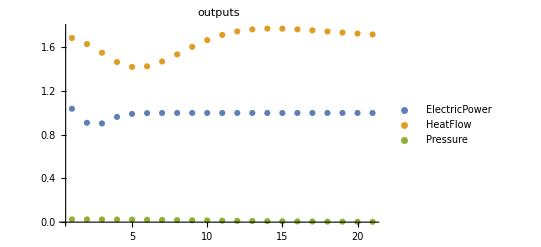

```mathematica
Tspan = 20.0;  
timecourse = Table[
{Subscript[h, 1][xt],Subscript[h, 2][xt],Subscript[h̄, 2][xt]}/.parameter/.CalLocalRes[equilibriumpoint+{0,0,0,0,0,0,0.05,0,0,0,0,0.05,0.0},1.0,0,Tspan] ,
{t,0.0,Tspan,1}];
timecourse = Flatten[timecourse,1];
ListPlot[{timecourse[[All,1]], timecourse[[All,2]],timecourse[[All,3]]},
PlotLabel->"outputs",PlotLegends->{ElectricPower,HeatFlow,Pressure},PlotRange->Full]
```

```mathematica
ListPlot[{timecourse[[All,1]], timecourse[[All,2]],timecourse[[All,3]]},
PlotLabel->"outputs",PlotLegends->{ElectricPower,HeatFlow,Pressure},PlotRange->Full]
```

-Graphics-

## 3. Design of Upper-level MPC controller

### Preliminary: Derivatives used for linearization of the model

```mathematica
Subscript[dΦ, param][xfun]= dΦ[xarg]/.parameter;
Subscript[dr, param][xfun] = dr[xarg]/.parameter;
```

```mathematica
dqdξ[x_] = Module[{drdx, dΦdx, return},

drdx = Subscript[dr, param][x];
dΦdx= Subscript[dΦ, param][x];
return = drdx.Inverse[dΦdx] 
];dqdξ[equilibriumpoint];
```

```mathematica
Module[{po1,po2,poles,s,coef,αξlist,stabilize,input},
po1=2.5;po2=0.25;
poles={Expand[(s+po1)^5],Expand[( s+po2)^3]};coef={CoefficientList[poles⟦1⟧,{s}],CoefficientList[poles⟦2⟧,{s}]};
αξlist={Table[coef⟦1,j⟧ ξ[xarg]⟦1,j⟧,{j,γ[[1]]}],Table[coef⟦2,j⟧ ξ[xarg]⟦2,j⟧,{j,γ[[2]]}]};
stabilize={-Total[αξlist⟦1⟧],-Total[αξlist⟦2⟧]};
input=Inverse[A[xarg]].{-Lf5h1[xarg]+stabilize⟦1⟧,-Lf3h2[xarg]+stabilize⟦2⟧};
dudx[xfun]=D[input,{xarg}] /. parameter;
]
dudx[equilibriumpoint];
```

```mathematica
dudξ[x_] := Module[{invA, dAinvdx,return},
return = dudx[x].Inverse[Subscript[dΦ, param][x]]
];
dudv[x_]:=Inverse[A[x]].{{coef⟦1,1⟧,0},{0,coef⟦2,1⟧}}/.parameter;
```

```mathematica
dudv[equilibriumpoint]
```

{{0.0164584,-0.00184292},{-0.0164584,0.00393132}}

### Linearized model (Continuous ẋ = A_cx + B_cv and Discrete x_(n+1)= A_dx_n + B_d v_n )

```mathematica
Ae=Join[Join[ConstantArray[0,{γ⟦1⟧-1,1}],IdentityMatrix[γ⟦1⟧-1],2],{-coef⟦1,1;;γ⟦1⟧⟧}];
Ah=Join[Join[ConstantArray[0,{γ⟦2⟧-1,1}],IdentityMatrix[γ⟦2⟧-1],2],{-coef⟦2,1;;γ⟦2⟧⟧}];
Ac[x_]:=Module[{Aeaug,Ahaug,return},Aeaug=Join[Ae,ConstantArray[0,{γ⟦1⟧,n-γ⟦1⟧}],2];Ahaug=Join[ConstantArray[0,{γ⟦2⟧,γ⟦1⟧}],Ah,ConstantArray[0,{γ⟦2⟧,n-γ⟦1⟧-γ⟦2⟧}],2];return=Join[Aeaug,Ahaug,dqdξ[x]]]
Bc[x_]:=Module[{Acx,Bin,Bin1,Bin2,Bec,Bhc,return},
Bec=-Ae.Join[{{1}},Table[{0},γ⟦1⟧-1]];Bhc=-Ah.Join[{{1}},Table[{0},γ⟦2⟧-1]];Bin1=Join[Bec,Table[{0},n-γ⟦1⟧]];Bin2=Join[Table[{0},γ⟦1⟧],Bhc,Table[{0},n-γ⟦1⟧-γ⟦2⟧]];return=Join[Bin1,Bin2,2]];
MatrixForm[Ac[equilibriumpoint]] (* Linearization at equilibrium point *)
MatrixForm[Bc[equilibriumpoint]];
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-97.6563 | -195.313 | -156.25 | -62.5 | -12.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.015625 | -0.1875 | -0.75 | 0 | 0 | 0 | 0 | 0
12.1922 | 1.36027 | 0.662961 | 0.0648855 | 0. | 0. | -45.4095 | 0. | -10. | -2.79318 | -1.21442 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.34783 | 0. | 0.
2.26967 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.46979 | -7.30902 | -0.217391 | 0. | 0.
0.947731 | 0.105738 | 0.0515338 | 0.00504373 | 0. | 0. | -5.52981 | 0. | -2.10346×10^-17 | -0.217121 | -0.0944006 | 0. | -1.08309
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.15625 | -0.50438)

```mathematica
Subscript[T, s] = 2; (* sampling time of descretization *)
AdBd [x_] := Module[{AB, AB00, M, Ad, Bd, return},
AB=Join[Ac[x],Bc[x],2];
AB00 = Join[AB, ConstantArray[0,{2,n+2}]];
M = MatrixExp[AB00*Subscript[T, s]];
Ad = M[[1;;n,1;;n]];
Bd= M[[1;;n,n+1;;n+2]];
return ={Ad,Bd}
];
MatrixForm[AdBd[equilibriumpoint][[1]]];
MatrixForm[AdBd[equilibriumpoint][[2]]];
```

### MPC Problem with Linearized model

```mathematica
Hu1 = 5; (* Control Horizon for Electricity *)
Hu2 = 5; (* Control Horizon for Heat *)
Hp = 10; (* Prediction Horizon *)
(* inputs = Flatten[ Table[{Subscript[u, i,1],Subscript[u, i,2]},{i,Hu}]]; *)
inputs = Join[Table[Subscript[v, i,1],{i,Hu1}],Table[Subscript[v, i,2],{i,Hu2}]];
```

```mathematica
inputs1 = Join[Table[{Subscript[v, i,1]},{i,Hu1}],Table[{Subscript[v, Hu1,1]},Hp-Hu1]];
inputs2 = Join[Table[{Subscript[v, i,2]},{i,Hu2}],Table[{Subscript[v, Hu2,2]},Hp-Hu2]];
(* inputs2 = Table[{Subscript[u, 1,2]},Hpp]; *)
inputSequence = Flatten[Join[inputs1,inputs2,2]]
```

{v_(1,1),v_(1,2),v_(2,1),v_(2,2),v_(3,1),v_(3,2),v_(4,1),v_(4,2),v_(5,1),v_(5,2),v_(5,1),v_(5,2),v_(5,1),v_(5,2),v_(5,1),v_(5,2),v_(5,1),v_(5,2),v_(5,1),v_(5,2)}

```mathematica
xk[AdBd_,xo_,k_]:=Module[{Ad,Bd, Adpower,AdBdsequence,AdBdmatrix, return},
Ad = AdBd[[1]];
Bd =AdBd[[2]];
Adpower = MatrixPower[Ad,k];
AdBdsequence= Nest[Join[Ad.# ,Bd,2]&,Bd,k-1];
AdBdmatrix = Join[AdBdsequence,ConstantArray[0,{n,(Hp-k)*2}],2];
return = Adpower.xo + AdBdmatrix.inputSequence
]; 
xk[AdBd[equilibriumpoint],Table[{0},n],3];
```

```mathematica
trimcondition[y1ref_,y2ref_,Δy2ref_] := Module[{trimeq, tr,  xtrim},
trimeq=Join[(ξ[xarg]⟦1⟧ -{y1ref,0,0,0,0}), 
		    (ξ[xarg]⟦2⟧- {y2ref-coef⟦2,2⟧/coef⟦2,1⟧* Δy2ref, Δy2ref, 0}),
                       ( r[xarg]) 
		   ]/.parameter ;
tr=FindRoot[trimeq==0,
{{x1,0.7},{x2,0.7},{x3,0.7},{x4,0.7},{x5,0.7},{x6,0.7},{x7,0.3},{x8,0},{x9,0.3},{x10,0},{x11,0},{x12,0},{x13,0}}];
xtrim = xarg/. tr
]
trimcondition[1.0,0.1,0.00]
Φ[trimcondition[1.0,0.00,0.012]]/.parameter
```

{0.614444,0.614444,0.614444,0.552222,0.552222,0.552222,0.663523,0.,0.394237,0.,0.262816,-0.0628157,0.201752}

{1.,0.,7.16596×10^-17,-1.55782×10^-17,-3.66234×10^-15,-0.144,0.012,0.,0.573278,0.61679,0.,0.180116,0.150048}

```mathematica
MPCsolver[x_,pref_,y1nom_,y2nom_,Δy2nom_]:=Module[{AB,X0, Ξ,Ξ0,states,return},
(* Derive trim condition and linearized model *)
xtrim = trimcondition[y1nom,y2nom,Δy2nom];
AB = AdBd[xtrim]; (* A and B matrix of the model for MPC *)

(* Derive current state in error coordinate  *)
Ξ = Φ[x]/.parameter  ; (* current state *)
Ξ0 = Φ[xtrim]/.parameter;
X0 = Ξ -Ξ0;  (* initial condition *)

(* MPC formulation 1: Describe states and outputs by input variables *)

states = Table[xk[AB,X0,k],{k,Hp}];
Cpower = Join[{1,0,0,0,0},Table[0,n-γ⟦1⟧]]; (* C matrix for y1*)
Cheat = Join[Table[0,γ⟦1⟧],Table[0,γ⟦2⟧],{0,0,0,0,1}]; (* C matrix for y2 (velocity w) *)
Cpressure = Join[Table[0,γ⟦1⟧],{1,0,0},{0,0,0,0,0}];   (* C matrix for pressure *)
Ypower = Flatten[Table[(Cpower.states⟦k⟧+Ξ0⟦1⟧),{k,Hp}]];
Yheat = Flatten[Table[Cheat.states[[k]]+Ξ0⟦13⟧,{k,Hp}]];
Ypressure = Flatten[Table[Cpressure.states[[k]]+Ξ0⟦6⟧,{k,Hp}]];

(* Cost function *)
Perror= Table[Ypower[[k]]-pref⟦k⟧,{k,Hp}];
inputdev = Table[(Subscript[v, i,1]-Subscript[v, i+1,1])^2,{i,Hu1-1}];
epdev =Table[states⟦k⟧.DiagonalMatrix[{1,1,1,1,1,1,1,1,1,1,1,1,1000}].states⟦k⟧,{k,Hp}];
costfunc=1000*Total[Perror^2]+ 0*Total[inputdev]+1.0*Total[epdev];

(* Constraints *)
ConcatConstraints[conditions_ ] := Module[{conds, stackedconds},
conds = True;
For[ i=1,i≤Length[conditions],i++,conds=And[conds,conditions[[i]]]];
stackedconds = conds
];
maxflow = 60/Subscript[w, rated];
maxpressure = 50*1000 /Subscript[p, rated];CondHeat = ConcatConstraints[Table[Yheat[[k]]>maxflow/3 && Yheat[[k]]<maxflow,{k,Hp}]]; 
CondPressure = ConcatConstraints[Table[Ypressure[[k]]>-maxpressure&& Ypressure[[k]]<maxpressure,{k,Hp}]];
(* CondFuel = ConcatConstraints[Table[Yfuel[[k]]>0 && Yfuel[[k]]<1,{k,2*Hp}]]; *)
(* CondInput = ConcatConstraints[Table[Subscript[u, i,2]-Subscript[u, i+1,2]<0.1,{i,Hu-1}]]; *)
constraints = Join[CondPressure];

(* Optimization *)
minimum = FindMinimum[{costfunc,constraints},inputs];
v1 =(Table[Subscript[v, i,1],{i,Hu1}] /.minimum⟦2⟧); 
v2 =(Table[Subscript[v, 1,2],{i,Hu2}] /.minimum⟦2⟧);
return ={v1,v2}
]
MPCsolver[equilibriumpoint,Table[1.1,10],1.0, 0, 0]
maxflow
maxpressure
```

{{0.173757,0.0536238,0.125668,0.087515,0.100152},{0.76335,0.76335,0.76335,0.76335,0.76335}}

1.92

12.3077

### Test of MPC Solver

```mathematica
SysDiscrete = StateSpaceModel[{AdBd[equilibriumpoint][[1]],AdBd[equilibriumpoint][[2]],{Cpower,Cheat,Cpressure}}, SamplingPeriod->2];
Module[{pref,refs,output, Δy2nom},
pref = {1.0,1.0,1.0,1.0,1.1,1.1,1.1,1.1,1.1,1.1};
Δy2nom = 0.02;
refs = {MPCsolver[equilibriumpoint,pref,1.0,0,Δy2nom][[1]]-1.0, MPCsolver[equilibriumpoint,pref,1.0,0,Δy2nom][[2]]-0};
output = OutputResponse[ SysDiscrete,refs];
Print[refs];
Print[output];
]
```

{{-1.0093,-0.981692,-1.03429,-0.946672,-0.89779},{2.69653,2.69653,2.69653,2.69653,2.69653}}

{{0.,-0.564713,-0.964331,-1.01106,-0.983733},{0.,-0.0321806,-0.284366,-0.717532,-1.12854},{0.,0.0387968,0.216535,0.51545,0.871851}}

## 4. Simulation of the Closed-loop System

This section performs simulation of the closed-loop system.

### Signal of ancillary service

```mathematica
(* ASsignal[t_]:= 1.0+ 0.1*Sin[2π*t/30]; (* ancillary service signal *) *)
SetDirectory[NotebookDirectory[]];
regd = Import["reg-d.CSV"];
regd = Join[regd,Table[regd⟦1202⟧, {i,5}]];  (* padding for 2400s to 2410s*)
ASsignal[t_] := 1.0 + 0.1*regd⟦2+t/2,2⟧
Table[ASsignal[2*i], {i, 0, 5}]
```

{1.00063,1.00063,0.999566,0.998108,0.995666,0.992843}

### Nominal references and signal of ancillary service

0.192

{0.606726,0.606726,0.606726,0.571519,0.571519,0.571519,0.654615,0.,0.401877,0.,0.120545,-0.174545,0.192058}

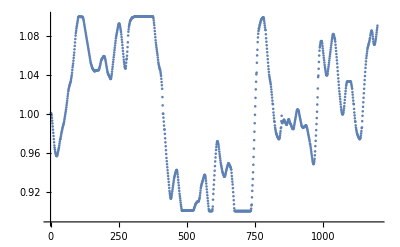

```mathematica
W = 6/Subscript[w, rated]
Δy2nom = 0.00225; 
y1nom[t_]:= 1.0;
y2nom[t_]:= 0 +Δy2nom *t ; 
trimcondition[y1nom[0],y2nom[0],Δy2nom]
ListPlot[Table[ASsignal[2*i], {i, 0, 1200}]]
```

### Module for calculation of each step

```mathematica
NextXt[time_,xt_]:=Module[{refPower,nextstate,v1v2,refs,return, resLocal, trajectory},

(* ancirally service signal is known for future 5 steps *)
refPower = Join[Table[ASsignal[time+Subscript[T, s]*i],{i,1,5}],Table[y1nom[time],Hp-5]];

(* MPC calculation *)
resMPC = MPCsolver[xt,refPower,y1nom[time],y2nom[time],Δy2nom ]; 
v1v2 = resMPC⟦1;;2,1⟧; (* calculated reference signals *)

(* Simulation of lower-level closed-loop system *)
y1ref = y1nom[time] + v1v2⟦1⟧;
y2ref = y2nom[time] + v1v2⟦2⟧;
resLocal = CalLocalRes[xt,y1ref,y2ref, Subscript[T, s]];
nextstate = Flatten[Table[Subscript[x, i][2.0],{i,n}]/.resLocal ];

(* Retrun results *)
return ={v1v2,{y1ref,y2ref}, nextstate,resLocal}
];
NextXt[0,equilibriumpoint];
```

### Simulation of closed-loop system

```mathematica
stepnum = 1200; (* number of steps *)
(* initialstate = equilibriumpoint+Join[Table[0,10],{0,0,0}]; *) 
initialstate = trimcondition[y1nom[0],y2nom[0],Δy2nom];
states = {initialstate};
MPCinputs = {};
outputdata = {{"time","v1","v2","ref1","ref2","power","pressure","velocity"}};
Module[{k,time,nextstep,v1v2,refs,state,trajectory,timecourse},
state=initialstate;
For[k=0,k<stepnum,k++,
time= 2*k;
(* calculation of next step*)
nextstep = NextXt[time,state];
v1v2 = nextstep⟦1⟧;
refs = nextstep⟦2⟧;
state = nextstep⟦3⟧;
trajectory = nextstep⟦4⟧;
(* log *)
timecourse = Flatten[Table[
Join[{time+t},v1v2,refs,{Subscript[h, 1][xt],Subscript[h̄, 2][xt],xt⟦13⟧}]/.parameter/.trajectory,
{t,0.0,2.0,0.5}],1];  (*  time course of output variables *)
MPCinputs = Append[MPCinputs,v1v2];
states = Append[states,state];
outputdata = Join[outputdata, timecourse] 
]
]
```

$Aborted

```mathematica
profPower = Table[{k,Subscript[h, 1][states⟦k⟧]},{k,stepnum}] /. parameter;
profpressure = Table[{k,Subscript[h̄, 2][states⟦k⟧]},{k,stepnum}] /. parameter;
profvelocity = Table[{k,states⟦k⟧⟦13⟧},{k,stepnum}] /. parameter;
V1= Table[{k,MPCinputs⟦k,1⟧},{k,stepnum}] /. parameter;V2 = Table[{k,MPCinputs⟦k,2⟧},{k,stepnum}] /. parameter;
ListPlot[{V1,profPower,V2,profvelocity,profpressure},PlotLabel->"output",
PlotLegends->{Subscript[v, 1],Subscript[y, 1]( electric power),Subscript[v, 2],Subscript[y, 2](velocity),pressure},
PlotMarkers-> {"+","o","+","o","o"},
PlotRange->Full]
```

-Graphics-

#### Export Data

```mathematica
(* SetDirectory[NotebookDirectory[]];
Export["mpc.csv",outputdata] )*
```

mpc.csv